## 8 State Telegraph with equal populations

### Getting the full expression for the turnovers probabilities

```mathematica
W={{-l,0,0,0,0,0,0,r},{l,-r,0,0,0,0,0,0},{0,r,-l,0,0,0,0,0},{0,0,l,-r,0,0,0,0},
{0,0,0,r,-l,0,0,0},{0,0,0,0,l,-r,0,0},{0,0,0,0,0,r,-l,0},{0,0,0,0,0,0,l,-r}};
MatrixForm[W]
us=Eigenvectors[W];
ls=Eigenvalues[W]
```

(-l | 0 | 0 | 0 | 0 | 0 | 0 | r
l | -r | 0 | 0 | 0 | 0 | 0 | 0
0 | r | -l | 0 | 0 | 0 | 0 | 0
0 | 0 | l | -r | 0 | 0 | 0 | 0
0 | 0 | 0 | r | -l | 0 | 0 | 0
0 | 0 | 0 | 0 | l | -r | 0 | 0
0 | 0 | 0 | 0 | 0 | r | -l | 0
0 | 0 | 0 | 0 | 0 | 0 | l | -r)

{0,-l-r,1/2 (-l-r-√(l^2-6 l r+r^2)),1/2 (-l-r+√(l^2-6 l r+r^2)),1/2 (-l-r-√(l^2-(2+4 ⅈ) l r+r^2)),1/2 (-l-r+√(l^2-(2+4 ⅈ) l r+r^2)),1/2 (-l-r-√(l^2-(2-4 ⅈ) l r+r^2)),1/2 (-l-r+√(l^2-(2-4 ⅈ) l r+r^2))}

```mathematica
(*Diagonalization check*)
U=Transpose[us];
Uinv=FullSimplify[Inverse[U]];
FullSimplify[Dot[Uinv,Dot[W,U]]]
```

{{0,0,0,0,0,0,0,0},{0,-l-r,0,0,0,0,0,0},{0,0,1/2 (-l-r-√(l^2-6 l r+r^2)),0,0,0,0,0},{0,0,0,1/2 (-l-r+√(l^2-6 l r+r^2)),0,0,0,0},{0,0,0,0,1/2 (-l-r-√(l^2-(2+4 ⅈ) l r+r^2)),0,0,0},{0,0,0,0,0,1/2 (-l-r+√(l^2-(2+4 ⅈ) l r+r^2)),0,0},{0,0,0,0,0,0,1/2 (-l-r-√(l^2-(2-4 ⅈ) l r+r^2)),0},{0,0,0,0,0,0,0,1/2 (-l-r+√(l^2-(2-4 ⅈ) l r+r^2))}}

```mathematica
DExp={{Exp[ls[[1]] t],0,0,0,0,0,0,0},{0,Exp[ls[[2]]  t],0,0,0,0,0,0},{0,0,Exp[ls[[3]]  t],0,0,0,0,0},{0,0,0,Exp[ls[[4]]  t],0,0,0,0},{0,0,0,0,Exp[ls[[5]]  t],0,0,0},{0,0,0,0,0,Exp[ls[[6]]  t],0,0},{0,0,0,0,0,0,Exp[ls[[7]]  t],0},{0,0,0,0,0,0,0,Exp[ls[[8]]  t]}};
MatrixForm[DExp]
PT=FullSimplify[Dot[U,FullSimplify[Dot[DExp,Uinv]]]];
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅇ^((-l-r) t) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅇ^(1/2 (-l-r-√(l^2-6 l r+r^2)) t) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅇ^(1/2 (-l-r+√(l^2-6 l r+r^2)) t) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅇ^(1/2 (-l-r-√(l^2-(2+4 ⅈ) l r+r^2)) t) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅇ^(1/2 (-l-r+√(l^2-(2+4 ⅈ) l r+r^2)) t) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(1/2 (-l-r-√(l^2-(2-4 ⅈ) l r+r^2)) t) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(1/2 (-l-r+√(l^2-(2-4 ⅈ) l r+r^2)) t))

```mathematica
DExpStat={{1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}};
PStat=FullSimplify[Dot[Dot[U,Dot[DExpStat,Uinv]],{a,b,c,d,e,f,g,1-a-b-c-d-e-f-g}]]
```

{r/(4 (l+r)),l/(4 (l+r)),r/(4 (l+r)),l/(4 (l+r)),r/(4 (l+r)),l/(4 (l+r)),r/(4 (l+r)),l/(4 (l+r))}

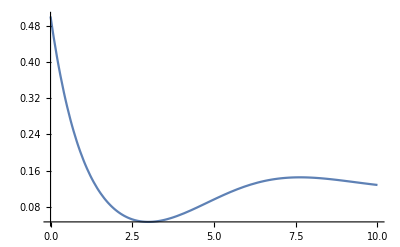

```mathematica
lv=1;
rv=1;
P0={0.5,0.35,0.1,0.05,0,0,0,0};
Traj=FullSimplify[Dot[PT/.{l->lv,r->rv},P0]];
Plot[{Re[Traj[[1]]]},{t,0,10},PlotRange->All]
```

```mathematica
P0={1,0,0,0,0,0,0,0};
FullSimplify[Dot[PT,P0][[2]]]
```

1/4 l (1/(l+r)-ⅇ^(-((l+r) t))/(l+r)+(ⅇ^(1/2 (-l-r+√(l^2-6 l r+r^2)) t))/(√(l^2-6 l r+r^2))-(ⅇ^(-1/2 (l+r+√(l^2-6 l r+r^2)) t))/(√(l^2-6 l r+r^2))+(ⅇ^(1/2 (-l-r+√(l^2-(2+4 ⅈ) l r+r^2)) t))/(√(l^2-(2+4 ⅈ) l r+r^2))-(ⅇ^(-1/2 (l+r+√(l^2-(2+4 ⅈ) l r+r^2)) t))/(√(l^2-(2+4 ⅈ) l r+r^2))+(ⅇ^(1/2 (-l-r+√(l^2-(2-4 ⅈ) l r+r^2)) t))/(√(l^2-(2-4 ⅈ) l r+r^2))-(ⅇ^(-1/2 (l+r+√(l^2-(2-4 ⅈ) l r+r^2)) t))/(√(l^2-(2-4 ⅈ) l r+r^2)))

```mathematica
PTurn=FullSimplify[
PStat[[1]](PT[[5]][[1]]+PT[[6]][[1]]+PT[[7]][[1]]+PT[[8]][[1]])+
PStat[[2]](PT[[5]][[2]]+PT[[6]][[2]]+PT[[7]][[2]]+PT[[8]][[2]])+
PStat[[3]](PT[[5]][[3]]+PT[[6]][[3]]+PT[[7]][[3]]+PT[[8]][[3]])+
PStat[[4]](PT[[5]][[4]]+PT[[6]][[4]]+PT[[7]][[4]]+PT[[8]][[4]])+
PStat[[5]](PT[[1]][[5]]+PT[[2]][[5]]+PT[[3]][[5]]+PT[[4]][[5]])+
PStat[[6]](PT[[1]][[6]]+PT[[2]][[6]]+PT[[3]][[6]]+PT[[4]][[6]])+
PStat[[7]](PT[[1]][[7]]+PT[[2]][[7]]+PT[[3]][[7]]+PT[[4]][[7]])+
PStat[[8]](PT[[1]][[8]]+PT[[2]][[8]]+PT[[3]][[8]]+PT[[4]][[8]])
];
PTurnAV=FullSimplify[
PStat[[1]](PT[[5]][[1]]+PT[[6]][[1]])+
PStat[[2]](PT[[5]][[2]]+PT[[6]][[2]])+
PStat[[3]](PT[[7]][[3]]+PT[[8]][[3]])+
PStat[[4]](PT[[7]][[4]]+PT[[8]][[4]])+
PStat[[5]](PT[[1]][[5]]+PT[[2]][[5]])+
PStat[[6]](PT[[1]][[6]]+PT[[2]][[6]])+
PStat[[7]](PT[[3]][[7]]+PT[[4]][[7]])+
PStat[[8]](PT[[3]][[8]]+PT[[4]][[8]])
];
```

### Looking for a compact expression for the turnover correlation

0.0001

0.00310667

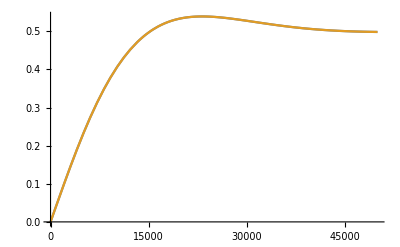

```mathematica
q=l+r;
k=√(l^2-6 l r+r^2);
k1=Sqrt[(l-r)^4+(4 l r)^2];
kp=Sqrt[(k1+(l-r)^2)/2];
km=Sqrt[(k1-(l-r)^2)/2];
C1=(kp(l^2+r^2)+2km l r)Cos[km/2 t];
C2=q k1 Cos[km/2 t];
S=(km(l^2+r^2)-2 kp l r)Sin[km/2 t];
G=C2-C1+S;
H=C1+C2+S;
PTurnEasy=1/(4q k1) (2 q k1-ⅇ^(-q/2 t)(ⅇ^(-1/2 kp t)G+ⅇ^(+1/2 kp t)H));
mu=0.00002;
n=1000;
s=0.005;
lv=mu n s
rv=s/Log[n s]
Plot[{PTurn/.{l->lv,r->rv},PTurnEasy/.{l->lv,r->rv}},{t,0,50000}]
```

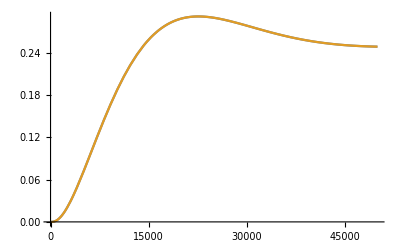

```mathematica
F=q Cosh[1/2 k t]+((l-r)^2 Sinh[1/2 k t])/k;
PTurnAVEasy=1/(4 q)(q+ⅇ^(-1/2 q t) (F-1/k1(ⅇ^(-1/2 kp t)G+ⅇ^(+1/2 kp t)H)));
Plot[{PTurnAV/.{l->lv,r->rv},PTurnAVEasy/.{l->lv,r->rv}},{t,0,50000}]
```

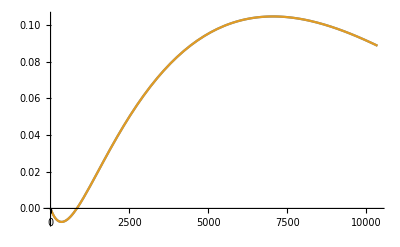

```mathematica
aux=ⅇ^(-q t)/(4 q k1^2)(ⅇ^(-1/2 kp t)G+ⅇ^(+1/2 kp t)H)^2;
covEasy=1/(4 q)(ⅇ^(-q/2 t)F -aux);
normEasy=(q-aux)/4/q;
corrEasy=(ⅇ^(-q/2 t)F -aux)/(q-aux);
maxScale=1/(q-kp)/.{l->lv,r->rv};
Plot[{((PTurnAV-PTurn^2)/PTurn/(1-PTurn))/.{l->lv,r->rv},corrEasy/.{l->lv,r->rv}},{t,0,2maxScale},PlotRange->All]
```